## INITIALIZATION

```mathematica
dec8pics=Import/@FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 8 2016\\**\\.tif"];
dec8files=FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 8 2016\\**.tif"];
```

```mathematica
dec9pics=Import/@FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 9 2016\\**.tif"];
dec9files=FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 9 2016\\**.tif"];
```

```mathematica
dec10pics=Import/@FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 10 2016\\**\\**\\**.tif"];
dec10files=FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 10 2016\\**\\**\\**.tif"];
```

```mathematica
dec12pics=Import/@FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 12 2016\\**\\**\\**.tif"];
dec12files=FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 12 2016\\**\\**\\**.tif"];
```

```mathematica
dec13pics=Import/@FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 13 2016\\**\\**\\**.tif"];
dec13files=FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 13 2016\\**\\**\\**.tif"];
```

```mathematica
dec14pics=Import/@FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 14 2016\\**\\**\\**.tif"];
dec14files=FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 14 2016\\**\\**\\**.tif"];
```

```mathematica
GGroupDec14=Import/@FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 14 2016\\Girls Group\\**\\**.tif"];
GGroupDec14files=FileNames["C:\\Users\\student\\Documents\\Cancer Bio Pics\\December 14 2016\\Girls Group\\**\\**.tif"];
GGroupDec14adj=ImageAdjust/@GGroupDec14[[All,1]];
```

```mathematica
allpics=Flatten[Join[{If[Length[#]==2,#[[1]],#]&/@dec8pics,If[Length[#]==2,#[[1]],#]&/@dec9pics,If[Length[#]==2,#[[1]],#]&/@dec10pics,If[Length[#]==2,#[[1]],#]&/@dec12pics,If[Length[#]==2,#[[1]],#]&/@dec14pics}]];
```

```mathematica
allpicsadj=ImageAdjust/@allpics;
```

```mathematica
allfiles=Flatten[Join[{dec8files,dec9files,dec10files,dec12files,dec14files}]];
```

```mathematica
Mean[Flatten[ImageData[-Graphics-]]]
```

0.49232

```mathematica
Mean[Flatten[ImageData[-Graphics-]]]
```

0.419223

```mathematica
allpics[[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

# TEST FILE

ALL PICS

```mathematica
Manipulate[allpics[[i]],{i,1,Length[allpicsadj],1}]
```

Part::partd: Part specification allpics⟦41⟧ is longer than depth of object.

Part::partd: Part specification allpics⟦1⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::partd: Part specification allpics⟦1⟧ is longer than depth of object.

```mathematica
Manipulate[Mean[Flatten[ImageData[allpics[[i]]]]],{i,1,Length[allpics],1}]
```

Part::partd: Part specification allpics⟦154⟧ is longer than depth of object.

ImageData::imginv: Expecting an image or graphics instead of allpics⟦154⟧.

Part::partd: Part specification allpics⟦154⟧ is longer than depth of object.

ImageData::imginv: Expecting an image or graphics instead of allpics⟦154⟧.

Part::partw: Part 154 of {} does not exist.

ImageData::imginv: Expecting an image or graphics instead of {}⟦154⟧.

Part::partd: Part specification allpics⟦154⟧ is longer than depth of object.

ImageData::imginv: Expecting an image or graphics instead of allpics⟦154⟧.

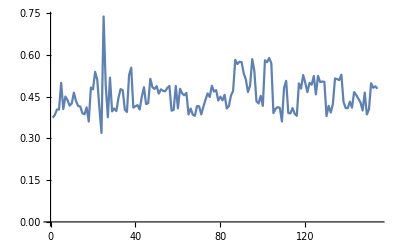

```mathematica
ListLinePlot[Table[Mean[Flatten[ImageData[allpics[[i]]]]],{i,1,Length[allpics],1}]]
```

Charcoal Filter

```mathematica
Manipulate[Binarize[(ImageEffect[allpics[[i]],#]&/@{"Charcoal"})[[1]]],{i,1,Length[allpics],1}]
```

Part::partd: Part specification allpics⟦88⟧ is longer than depth of object.

ImageEffect::imginv: Expecting an image or graphics instead of allpics⟦88⟧.

Binarize::imginv: Expecting an image or graphics instead of ImageEffect[allpics⟦88⟧,Charcoal].

Part::partd: Part specification allpics⟦88⟧ is longer than depth of object.

ImageEffect::imginv: Expecting an image or graphics instead of allpics⟦88⟧.

Binarize::imginv: Expecting an image or graphics instead of ImageEffect[allpics⟦88⟧,Charcoal].

Part::partd: Part specification allpics⟦88⟧ is longer than depth of object.

ImageEffect::imginv: Expecting an image or graphics instead of allpics⟦88⟧.

Binarize::imginv: Expecting an image or graphics instead of ImageEffect[allpics⟦88⟧,Charcoal].

```mathematica
charpics=Table[(ImageEffect[allpics[[i]],#]&/@{"Charcoal"})[[1]],{i,1,Length[allpics]}];
```

Dead Cell Finder

```mathematica
cells=SelectComponents[DeleteBorderComponents[Binarize[-Graphics-,{0,.5}]],#EnclosingComponentCount==1&];
circles=ComponentMeasurements[ImageMultiply[-Graphics-,cells],{"Centroid","EquivalentDiskRadius"}][[All,2]];
Show[-Graphics-,Graphics[{Red,Thick,Circle@@#&/@circles}]]
```

-Graphics-

Select Components (Dead Cells)

```mathematica
cells=SelectComponents[Binarize[-Graphics-,{0,.5}],{"Area","Holes"},60<#1<750&&#2>0||#2>1&];
circles=ComponentMeasurements[cells,{"Centroid","EquivalentDiskRadius"}][[All,2]];
Show[-Graphics-,Graphics[{Red,Thick,Circle@@#&/@circles}]]
```

-Graphics-

```mathematica
cells=SelectComponents[Binarize[-Graphics-],{"Area","Holes"},60<#1<750&&#2>0||#2>1&];
circles=ComponentMeasurements[cells,{"Centroid","EquivalentDiskRadius"}][[All,2]];
Show[-Graphics-,Graphics[{Red,Thick,Circle@@#&/@circles}]]
```

-Graphics-

```mathematica
FindClusters
```

```mathematica
cells=SelectComponents[Binarize[-Graphics-,{0,.5}],{"Area","Holes"},60<#1<500&&#2>0||#2>1&];
circles=ComponentMeasurements[cells,{"Centroid","EquivalentDiskRadius"}][[All,2]];
Show[-Graphics-,Graphics[{Red,Thick,Circle@@#&/@circles}]]
```

-Graphics-

Select Else

```mathematica
Row[{SelectComponents[Binarize[-Graphics-,{0,.5}],{"Area","Holes"},60<#1<750&&#2>0||#2>1&],SelectComponents[Binarize[-Graphics-,{0,.5}],{"Area","Holes"},#1<60||#1>750&&#2==0&]}]
```

-Graphics--Graphics-

Select Components (Noise)

```mathematica
cells=SelectComponents[Binarize[-Graphics-,{0,.5}],"Area",#1<100&];
circles=ComponentMeasurements[cells,{"Centroid","EquivalentDiskRadius"}][[All,2]];
Show[-Graphics-,Graphics[{Red,Thick,Circle@@#&/@circles}]]
```

-Graphics-

Select Else

```mathematica
SelectComponents[Binarize[-Graphics-,{0,.5}],"Area",#1>100&]
```

-Graphics-

```mathematica
cells=SelectComponents[Binarize[-Graphics-,{0,.5}],"Area",#1<100&];
circles=ComponentMeasurements[cells,{"Centroid","EquivalentDiskRadius"}][[All,2]];
Show[-Graphics-,Graphics[{Red,Thick,Circle@@#&/@circles}]]
```

-Graphics-

```mathematica
ImageSubtract[-Graphics-,SelectComponents[Binarize[-Graphics-,{0,.5}],"Area",#1<100&]]
```

-Graphics-

Combine Last 2 (one inside another)

```mathematica
SelectComponents[Binarize[ColorNegate[SelectComponents[Binarize[-Graphics-,{0,.5}],{"Area","Holes"},#1<60||#1>750&&#2==0&]],{0,.5}],"Area",#1>50&]
```

-Graphics-

```mathematica
SelectComponents[Binarize[ColorNegate[SelectComponents[Binarize[-Graphics-,{0,.5}],{"Area","Holes"},#1<40||#1>400&&#2==0&]],{0,.5}],"Area",#1>25&]
```

-Graphics-

```mathematica
Tally[Flatten[ImageData[-Graphics-]]]
```

{{0,467723},{1,12277}}

```mathematica
N[Tally[Flatten[ImageData[-Graphics-]]][[2,2]]/Total[Tally[Flatten[ImageData[-Graphics-]]][[All,2]]]]
```

0.0255771

```mathematica
SelectComponents[Binarize[ColorNegate[SelectComponents[Binarize[-Graphics-,{0,.5}],{"Area","Holes"},#1<60||#1>100&&#2==0&]],{0,.5}],"Area",#1>25&]
```

-Graphics-

```mathematica
Tally[Flatten[ImageData[-Graphics-]]]
```

{{0,443823},{1,36177}}

```mathematica
N[Tally[Flatten[ImageData[-Graphics-]]][[2,2]]/Total[Tally[Flatten[ImageData[-Graphics-]]][[All,2]]]]
```

0.0753688

SelectComponentsFunc1

```mathematica
scFunc1[img_]:=Block[{charc,selComp, finalcComp },charc=(ImageEffect[img,#]&/@{"Charcoal"})[[1]];selComp=SelectComponents[Binarize[ColorNegate[SelectComponents[Binarize[charc,{0,.5}],{"Area","Holes"},#1<60||#1>100&&#2==0&]],{0,.5}],"Area",#1>25&];finalcComp=N[Tally[Flatten[ImageData[selComp]]][[2,2]]/Total[Tally[Flatten[ImageData[selComp]]][[All,2]]]]]
```

```mathematica
tabsSCFUNC1=Table[scFunc1[allpics[[i]]],{i,1,Length[allpics],1}];
```

```mathematica
tabsFuncPic=Table[{tabsSCFUNC1[[i]],allpics[[i]]},{i,1,Length[allpics],1}];
```

```mathematica
tabsFuncFile=Table[{tabsSCFUNC1[[i]],allfiles[[i]]},{i,1,Length[allfiles],1}];
```

Part::partw: Part 155 of {0.0765354,0.0895896,0.0985771,0.103229,0.0511792,0.0455583,0.0556229,0.0444646,0.102533,0.0982396,0.0815479,0.0613104,0.0748604,0.0617292,0.0762188,0.0575104,0.0748729,0.0726208,0.0683417,0.0637271,«12»,0.0576188,0.0446396,0.0840417,0.0693958,0.0626646,0.0769646,0.0836167,0.0791313,0.0800938,0.100365,0.132119,0.141758,0.0329292,0.0668583,0.0603313,0.0931,0.0515396,0.054575,«104»} does not exist.

Part::partw: Part 156 of {0.0765354,0.0895896,0.0985771,0.103229,0.0511792,0.0455583,0.0556229,0.0444646,0.102533,0.0982396,0.0815479,0.0613104,0.0748604,0.0617292,0.0762188,0.0575104,0.0748729,0.0726208,0.0683417,0.0637271,«12»,0.0576188,0.0446396,0.0840417,0.0693958,0.0626646,0.0769646,0.0836167,0.0791313,0.0800938,0.100365,0.132119,0.141758,0.0329292,0.0668583,0.0603313,0.0931,0.0515396,0.054575,«104»} does not exist.

Part::partw: Part 157 of {0.0765354,0.0895896,0.0985771,0.103229,0.0511792,0.0455583,0.0556229,0.0444646,0.102533,0.0982396,0.0815479,0.0613104,0.0748604,0.0617292,0.0762188,0.0575104,0.0748729,0.0726208,0.0683417,0.0637271,«12»,0.0576188,0.0446396,0.0840417,0.0693958,0.0626646,0.0769646,0.0836167,0.0791313,0.0800938,0.100365,0.132119,0.141758,0.0329292,0.0668583,0.0603313,0.0931,0.0515396,0.054575,«104»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
tabsFuncFile//Grid
```

```mathematica
tabGISCFUNC1=Table[scFunc1[GGroupDec14[[i,1]]],{i,1,Length[GGroupDec14],1}];
```

```mathematica
tabsGIFuncPic=Table[{tabsGISCFUNC1[[i]],GGroupDec14[[i]]},{i,1,Length[GGroupDec14],1}];
```

```mathematica
tabsGIFuncFile=Table[{tabGISCFUNC1[[i]],GGroupDec14files[[i]]},{i,1,Length[GGroupDec14files],1}];
```

```mathematica
tabsGIFuncFile//Grid
```

0.0466625 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C1 A Picture 1 Anomaly.tif
0.0489479 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C1 A Picture 2.tif
0.0488125 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C1 A Picture 3.tif
0.0518896 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C1 B Picture 1.tif
0.058125 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C1 B Picture 2.tif
0.0452792 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C2 A Picture 1.tif
0.0461896 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C2 A Picture 2.tif
0.0457708 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C2 B Picture 1.tif
0.0418625 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\C group\Girls C2 B Picture 2.tif
0.0394333 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\MLL Group\Girls MLL2 A Picture 1.tif
0.050875 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\MLL Group\Girls MLL2 A Picture 2.tif
0.0356438 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\MLL Group\Girls MLL2 B Picture1.tif
0.0273542 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\MLL Group\Girls MLL2 B Picture2.tif
0.044325 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\P group\Girls P1 A Picture 1.tif
0.0579063 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\P group\Girls P1 A Picture 2.tif
0.0830833 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\P group\Girls P1 B Picture 1.tif
0.0549271 | C:\Users\student\Documents\Cancer Bio Pics\December 14 2016\Girls Group\P group\Girls P1 B Picture 2.tif

```mathematica
Manipulate[SortBy[tabsFuncPic,First][[i,2]],{i,1,Length[allpics],1}]
```

SortBy::normal: Nonatomic expression expected at position 1 in SortBy[tabsFuncPic,First].

Part::partw: Part 56 of SortBy[tabsFuncPic,First] does not exist.

SortBy::normal: Nonatomic expression expected at position 1 in SortBy[tabsFuncPic,First].

Part::partw: Part 153 of SortBy[tabsFuncPic,First] does not exist.

SortBy::normal: Nonatomic expression expected at position 1 in SortBy[tabsFuncPic,First].

Part::partw: Part 153 of SortBy[tabsFuncPic,First] does not exist.

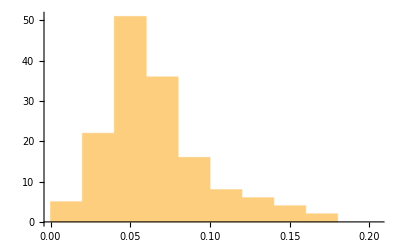

```mathematica
Histogram[tabsSCFUNC1]
```

```mathematica
allpics[[25]]
```

-Graphics-

```mathematica
allpics[[96]]
```

-Graphics-

```mathematica
Position[tabsSCFUNC1,Max[tabsSCFUNC1]]
```

{{25}}

```mathematica
Min[tabsSCFUNC1]
```

0.0126875

```mathematica
Position[tabsSCFUNC1,0.9478479166666667]
```

{{25}}

Select Components Try 2

```mathematica
SelectComponents[Binarize[-Graphics-,{0,.5}],{"AreaRadiusCoverage","Elongation","Area"},#1>.2&&#2>.4&]
```

-Graphics-

```mathematica
SelectComponents[Binarize[-Graphics-,{0,.5}],{"AreaRadiusCoverage","Elongation","Area"},#1>.2&&#2>.4&]
```

-Graphics-

Component Measurements

```mathematica
PairedHistogram[ComponentMeasurements[-Graphics-,"Holes"][[All,2]],ComponentMeasurements[-Graphics-,"Holes"][[All,2]]]
```

-Graphics-

```mathematica
PairedHistogram[ComponentMeasurements[-Graphics-,"AreaRadiusCoverage"][[All,2]],ComponentMeasurements[-Graphics-,"AreaRadiusCoverage"][[All,2]]]
```

-Graphics-

```mathematica
PairedHistogram[ComponentMeasurements[-Graphics-,"Elongation"][[All,2]],ComponentMeasurements[-Graphics-,"Elongation"][[All,2]]]
```

-Graphics-

```mathematica
PairedHistogram[ComponentMeasurements[-Graphics-,"AdjacentBorderCount"][[All,2]],ComponentMeasurements[-Graphics-,"AdjacentBorderCount"][[All,2]]]
```

-Graphics-

Binarize (Cluster)

```mathematica
Manipulate[Binarize[allpics[[i]],Method->"Cluster"],{i,1,Length[allpics],1}]
```

Part::partd: Part specification allpics⟦99⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of allpics⟦99⟧.

Part::partd: Part specification allpics⟦99⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of allpics⟦99⟧.

Part::partd: Part specification allpics⟦1⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of allpics⟦1⟧.

Delete Small Components (Cluster)

```mathematica
DeleteSmallComponents[-Graphics-,100,Method->"Cluster"]
```

-Graphics-

Gradient Filter

```mathematica
GradientFilter[allpicsadj[[145]],2]//ImageAdjust
```

-Graphics-

LaPlacGauss Filter

```mathematica
LaplacianGaussianFilter[allpicsadj[[145]],2]//ImageAdjust
```

-Graphics-

EdgeDetect

```mathematica
EdgeDetect[allpics[[10]]]
```

-Graphics-

Filling Transform

```mathematica
FillingTransform[EdgeDetect[allpics[[10]]]]
```

-Graphics-

Cluster Binarize

```mathematica
Manipulate[Binarize[allpics[[i]],Method->"Cluster"],{i,1,Length[allpics],1}]
```

Part::partd: Part specification allpics⟦25⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of allpics⟦25⟧.

Color Negate and Bin with Filling Transform

```mathematica
Manipulate[FillingTransform[ColorNegate[Binarize[allpics[[i]],.45,Method->"Cluster"]]],{i,1,Length[allpics],1}]
```

Set::write: Tag Times in {{{147.869,594.568},5.7259},{{42.6412,587.747},5.20157},«28»,{{554.826,24.9772},9.52462},{{555.417,25.4375},5.52791}} SelectComponents[Binarize[«1»],«1»,«1»&] is Protected.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

Part::partd: Part specification allpics⟦150⟧ is longer than depth of object.

Binarize::imginv: Expecting an image or graphics instead of allpics⟦150⟧.

ColorNegate::imginv: Binarize[allpics⟦150⟧,0.45,Method→Cluster] should be a valid image, a color directive, or a list of such objects.

FillingTransform::imginv: Expecting an image or graphics instead of ColorNegate[Binarize[allpics⟦150⟧,0.45,Method→Cluster]].

```mathematica
Manipulate[Length[ImageCorners[allpics[[i]]]],{i,1,Length[allpics],1}]
```

Part::partd: Part specification allpics⟦23⟧ is longer than depth of object.

ImageCorners::imginv: Expecting an image or graphics instead of allpics⟦23⟧.

```mathematica
Manipulate[Length[ImageKeypoints[allpics[[i]]]],{i,1,Length[allpics],1}]
```

Part::partd: Part specification allpics⟦152⟧ is longer than depth of object.

ImageKeypoints::imginv: Expecting an image or graphics instead of allpics⟦152⟧.

```mathematica
Manipulate[i=allpics[[1]];
corners=ImageCorners[i,j,k,v];
HighlightImage[i,corners],{j,0,10,.1},{k,0,10,.1},{v,0,10,.1}]
```

Part::partd: Part specification allpics⟦1⟧ is longer than depth of object.

ImageCorners::imginv: Expecting an image or graphics instead of allpics⟦1⟧.

HighlightImage::imginv: Expecting an image or graphics instead of allpics⟦1⟧.

```mathematica
i=allpics[[99]];
corners=ImageKeypoints[i];
HighlightImage[i,corners]
```

-Graphics-

```mathematica
Manipulate[Row[{CornerFilter[allpics[[i]],2]//ImageAdjust,allpics[[i]]}],{i,1,Length[allpics],1}]
```

```mathematica
Manipulate[Column[{ImageSaliencyFilter[allpics[[i]]]//ImageAdjust,allpics[[i]]}],{i,1,Length[allpics],1}]
```

Part::partd: Part specification allpics⟦12⟧ is longer than depth of object.

ImageSaliencyFilter::imginv: Expecting an image or graphics instead of allpics⟦12⟧.

ImageAdjust::imginv: Expecting an image or graphics instead of ImageSaliencyFilter[allpics⟦12⟧].

Part::partd: Part specification allpics⟦12⟧ is longer than depth of object.

ImageSaliencyFilter::imginv: Expecting an image or graphics instead of allpics⟦12⟧.

ImageAdjust::imginv: Expecting an image or graphics instead of ImageSaliencyFilter[allpics⟦12⟧].